# Illustration of harmonic spectrum

#### Color

```mathematica
color1=ColorData[71,1]
color2=ColorData[48,2]
color3=ColorData[24,5]
color4=ColorData[24,4]
color5=ColorData[34,3]
color6=ColorData[24,2]
color7=ColorData[24,3]
color8=ColorData[38,4]
```

Hue[0.94, 0.7, 0.9]

RGBColor[0.963806, 0.591257, 0.601724]

RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882]

RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843]

RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432]

RGBColor[1., 0.7215686274509804, 0.2196078431372549]

RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883]

RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961]

```mathematica
Table[ColorData[97,i],{i,1,10}]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]}

```mathematica
mycolorlistContrast={color1,color3,color5,color6,color7,color2,color4,color8}
mycolorlistSmooth={color1,color2,color7,color6,color4,color3}
mycolorlist={color1,color2,color3,color4,color5,color6,color7,color8}
mycolorlist4={RGBColor[0.14316, 0.646571, 0.600198],RGBColor[0.0885939, 0.437201, 0.00552377],RGBColor[0.54197, 0.776883, 0.148836],RGBColor[0.697017, 0.710521, 0.0335088],RGBColor[0.937911, 0.573907, 0.307698],RGBColor[0.961318, 0, 0.032517],RGBColor[0.196658, 0.311879, 0.853681]}
```

{Hue[0.94, 0.7, 0.9],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961]}

{Hue[0.94, 0.7, 0.9],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882]}

{Hue[0.94, 0.7, 0.9],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961]}

{RGBColor[0.14316, 0.646571, 0.600198],RGBColor[0.0885939, 0.437201, 0.00552377],RGBColor[0.54197, 0.776883, 0.148836],RGBColor[0.697017, 0.710521, 0.0335088],RGBColor[0.937911, 0.573907, 0.307698],RGBColor[0.961318, 0, 0.032517],RGBColor[0.196658, 0.311879, 0.853681]}

```mathematica
myRed=ColorData[112,1];
myBlue=ColorData[97,1];
mygreen=color8;
mycolorlistRedGrad=Table[Blend[{myRed,White},i/8],{i,1,8}]
mycolorlistGreenGrad=Table[Blend[{mygreen,White},i/8],{i,1,8}]
blendcolorlist=Join[{color3},Table[Blend[{color1,color6},i/8],{i,1,8}]]
tempcolorlist=Table[ColorData["TemperatureMap"][i],{i,0,1,0.25}]
mycolorlist3={ColorData["TemperatureMap"][0],color3,color7,color2,ColorData["TemperatureMap"][1]}
```

{RGBColor[0.8167645, 0.301029, 0.125],RGBColor[0.8429409999999999, 0.40088199999999996, 0.25],RGBColor[0.8691175, 0.500735, 0.375],RGBColor[0.895294, 0.600588, 0.5],RGBColor[0.9214705, 0.700441, 0.625],RGBColor[0.947647, 0.8002940000000001, 0.75],RGBColor[0.9738235, 0.900147, 0.875],RGBColor[1., 1., 1.]}

{RGBColor[0.4681372549019608, 0.763235294117647, 0.6362745098039216],RGBColor[0.5441176470588236, 0.7970588235294117, 0.6882352941176471],RGBColor[0.6200980392156863, 0.8308823529411764, 0.7401960784313726],RGBColor[0.696078431372549, 0.8647058823529412, 0.7921568627450981],RGBColor[0.7720588235294118, 0.8985294117647058, 0.8441176470588235],RGBColor[0.8480392156862746, 0.9323529411764706, 0.8960784313725491],RGBColor[0.9240196078431373, 0.9661764705882353, 0.9480392156862745],RGBColor[1., 1., 1.]}

{RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.9125, 0.32644607843137263, 0.4621509803921571],RGBColor[0.925, 0.38289215686274514, 0.4275019607843139],RGBColor[0.9375, 0.4393382352941177, 0.39285294117647074],RGBColor[0.95, 0.49578431372549026, 0.35820392156862757],RGBColor[0.9625, 0.5522303921568628, 0.3235549019607844],RGBColor[0.975, 0.6086764705882353, 0.28890588235294123],RGBColor[0.9875, 0.6651225490196078, 0.25425686274509807],RGBColor[1., 0.7215686274509804, 0.2196078431372549]}

{RGBColor[0.178927, 0.305394, 0.933501],RGBColor[0.642359, 0.720535, 0.964988],RGBColor[0.984192, 0.987731, 0.911643],RGBColor[0.955963, 0.863115, 0.283425],RGBColor[0.817319, 0.134127, 0.164218]}

{RGBColor[0.178927, 0.305394, 0.933501],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.817319, 0.134127, 0.164218]}

```mathematica
mycolorlist
```

{Hue[0.94, 0.7, 0.9],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961]}

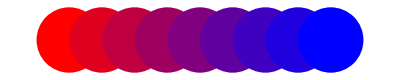

```mathematica
Graphics[Table[{Blend[{Red,Blue},x],Disk[{8 x,0}]},{x,0,1,1/8}]]
```

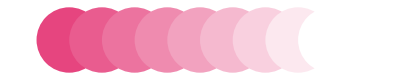

```mathematica
Graphics[Table[{Blend[{Hue[0.94, 0.7, 0.9],White},x],Disk[{8 x,0}]},{x,0,1,1/8}]]
```

```mathematica
Table[Blend[{Hue[0.94, 0.7, 0.9],White},x],{x,0,1,1/8}]
```

{RGBColor[0.9, 0.2700000000000001, 0.49680000000000024],RGBColor[0.9125, 0.36125000000000007, 0.5597000000000002],RGBColor[0.925, 0.45250000000000007, 0.6226000000000002],RGBColor[0.9375, 0.5437500000000001, 0.6855000000000002],RGBColor[0.95, 0.635, 0.7484000000000002],RGBColor[0.9625, 0.7262500000000001, 0.8113000000000001],RGBColor[0.975, 0.8175000000000001, 0.8742000000000001],RGBColor[0.9875, 0.90875, 0.9371],RGBColor[1., 1., 1.]}

```mathematica
Table[Blend[{RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],White},x],{x,0,1,1/8}]
```

{RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],RGBColor[0.4681372549019608, 0.763235294117647, 0.6362745098039216],RGBColor[0.5441176470588236, 0.7970588235294117, 0.6882352941176471],RGBColor[0.6200980392156863, 0.8308823529411764, 0.7401960784313726],RGBColor[0.696078431372549, 0.8647058823529412, 0.7921568627450981],RGBColor[0.7720588235294118, 0.8985294117647058, 0.8441176470588235],RGBColor[0.8480392156862746, 0.9323529411764706, 0.8960784313725491],RGBColor[0.9240196078431373, 0.9661764705882353, 0.9480392156862745],RGBColor[1., 1., 1.]}

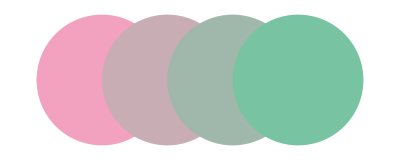

```mathematica
pinklist=Table[Blend[{RGBColor[0.95, 0.635, 0.7484000000000002],RGBColor[0.4681372549019608, 0.763235294117647, 0.6362745098039216]},x],{x,0,1,1/3}];
l=Length[pinklist];
Graphics[Table[{pinklist[[x]],Disk[{x,0}]},{x,1,l}]]
```

#### Font

```mathematica
font1="Times";
myfont="Times";
fontsizeXL=24;
fontsizeL=18;
fontsizeM=14;
fontsizeS=12;
fontsizeXS=10;
```

#### Cross section with v_1

```mathematica
f1[ϕ_,v1_,ψ1_]:=1/(2π)(1+2 v1 Cos[ϕ-ψ1])
```

```mathematica
Manipulate[
ParametricPlot[f1[ϕ,v1,ψ1]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,2π,π/4}
]
```

#### Calculate v_n from cross section by definition

```mathematica
FNvnx[f_,n_]:=NIntegrate[f[ϕ]Cos[n ϕ],{ϕ,0,2π}]
FNvny[f_,n_]:=NIntegrate[f[ϕ]Sin[n ϕ],{ϕ,0,2π}]
```

```mathematica
n=1;
ψn=.1;
vnx=NIntegrate[f1[ϕ,1,ψn]Cos[n ϕ],{ϕ,0,2π}]
vny=NIntegrate[f1[ϕ,1,ψn]Sin[n ϕ],{ϕ,0,2π}]
Sqrt[vnx^2+vny^2]
```

0.995004

0.0998334

1.

#### Cross section with v_n

```mathematica
FNfn[ϕ_,vn_,ψn_,n_]:=1/(2π)(1+2 vn Cos[n(ϕ-ψn)]);
FNfnnorm[vn_,ψn_,n_]:=NIntegrate[FNfn[ϕ,vn,ψn,n],{ϕ,0,2π}];
FNfnScaled[ϕ_,vn_,ψn_,n_]:=FNfn[ϕ,vn,ψn,n]/FNfnnorm[vn,ψn,n];
```

```mathematica
n=2;
ψn=.1;
vn=.2;
vnx=NIntegrate[FNfnScaled[ϕ,vn,ψn,n]Cos[n ϕ],{ϕ,0,2π}]
vny=NIntegrate[FNfnScaled[ϕ,vn,ψn,n]Sin[n ϕ],{ϕ,0,2π}]
Sqrt[vnx^2+vny^2]/vn
{ArcTan[vny/vnx],(ψn n),ψn+π/2}
```

0.196013

0.0397339

1.

{0.2,0.2,1.6708}

```mathematica
Manipulate[
ParametricPlot[FNfn[ϕ,v1,ψ1,2]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,π,π/4}
]
```

```mathematica
Manipulate[
ParametricPlot[FNfn[ϕ,v1,ψ1,3]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,2π/3,π/3}
]
```

```mathematica
Manipulate[
ParametricPlot[FNfn[ϕ,v1,ψ1,4]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,2π/4,π/4}
]
```

```mathematica
Manipulate[
ParametricPlot[FNfn[ϕ,v1,ψ1,5]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,2π/5,π/5}
]
```

#### Styled plot v_n

```mathematica
glabelFN=(Style[#,FontFamily->"Times New Roman",16,Black]&);
```

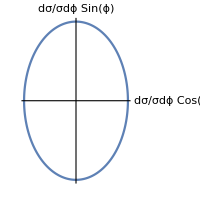
-Graphics-dσ/dϕ=σ/(2  π)

```mathematica
With[{v1=0,ψ1=0},
fig=ParametricPlot[
FNfn[ϕ,v1,ψ1,2]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},
ImageSize->200,
Ticks->None,
AxesLabel->glabelFN/@{"dσ/σdϕ Cos(ϕ)","dσ/σdϕ Sin(ϕ)"},
AxesStyle->Directive[Black]
];
Labeled[fig,Style["dσ/dϕ=σ/(2  π)",fontsizeL,FontFamily->font1,myBlue],Top]
]
```

```mathematica
With[{vn=0.3,ψn=π/3,n=1},
vnx=NIntegrate[FNfnScaled[ϕ,vn,ψn,n]Cos[n ϕ],{ϕ,0,2π}];
vny=NIntegrate[FNfnScaled[ϕ,vn,ψn,n]Sin[n ϕ],{ϕ,0,2π}];
fig=Show[
ParametricPlot[
FNfn[ϕ,vn,ψn,n]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},
ImageSize->200,
Ticks->None,
AxesLabel->glabelFN/@{"dσ/σdϕ Cos(ϕ)","dσ/σdϕ Sin(ϕ)"},
AxesStyle->Directive[Black],
Epilog->{Inset[Style["(v⃗)_1",fontsizeM+1,FontFamily->font1,myRed],Scaled[{.55,.8}]],
Inset[Style["ψ_1",fontsizeM,FontFamily->font1,myRed],Scaled[{.6,.4}]]
}
],
Graphics[{myRed,Arrowheads[Medium],Arrow[{{0,0},{vnx,vny}}]}],
Graphics[{myRed,Arrow[BSplineCurve[Table[{Cos[x],Sin[x]}vn/π/2,{x,0,ψn,ψn/10}]]]}]
];
Labeled[fig,Style[TraditionalForm["dσ/dϕ=σ/(2  π)[1+2v_1Cos(ϕ-ψ_1)]"],fontsizeL,FontFamily->font1,myBlue],Top]
]
```

-Graphics-dσ/dϕ=σ/(2  π)[1+2v_1Cos(ϕ-ψ_1)]

```mathematica
FNfn[ϕ,vn,ψn,n]
```

```mathematica
(1+2 vn Cos[2(0.1-ϕ)]+4 v4 Cos[4(ψ4-ϕ)])/(2 π)
```

```mathematica
With[{vn=0.3,ψn=π/3,n=2,v4=.1,ψ4=.3},
vnx=NIntegrate[FNfn[ϕ,vn,ψn,n]Cos[n ϕ],{ϕ,0,2π}];
vny=NIntegrate[FNfn[ϕ,vn,ψn,n]Sin[n ϕ],{ϕ,0,2π}];
fig=Show[
ParametricPlot[
FNfn[ϕ,vn,ψn,n]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},
ImageSize->180,
Ticks->None,
AxesLabel->glabelFN/@{"dσ/σdϕ Cos(ϕ)","dσ/σdϕ Sin(ϕ)"},
AxesStyle->Directive[Black],
Epilog->{Inset[Style["(v⃗)_2",fontsizeM+1,FontFamily->font1,myRed],Scaled[{.2,.8}]],
Inset[Style["ψ_2",fontsizeM,FontFamily->font1,myRed],Scaled[{.7,.6}]]
}
],
Graphics[{myRed,Arrowheads[Medium],Arrow[{{0,0},{vnx,vny}}]}],
Graphics[{myRed,Arrow[BSplineCurve[Table[{Cos[x],Sin[x]}vn/π/2,{x,0,ψn,ψn/10}]]]}],
Graphics[{myRed,Dashed,Line[{-{Cos[ψn],Sin[ψn]},{Cos[ψn],Sin[ψn]}}/π]}]
];
Labeled[fig,Style[TraditionalForm["dσ/dϕ=σ/(2  π)[1+2v_2Cos(2(ϕ-ψ_2))]"],fontsizeL,FontFamily->font1,myBlue],Top]
]
```

-Graphics-dσ/dϕ=σ/(2  π)[1+2v_2Cos(2(ϕ-ψ_2))]

```mathematica
With[{vn=0.3,ψn=π/3.2,n=3},
vnx=NIntegrate[FNfn[ϕ,vn,ψn,n]Cos[n ϕ],{ϕ,0,2π}];
vny=NIntegrate[FNfn[ϕ,vn,ψn,n]Sin[n ϕ],{ϕ,0,2π}];
fig=Show[
ParametricPlot[
FNfn[ϕ,vn,ψn,n]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},
ImageSize->200,
Ticks->None,
AxesLabel->glabelFN/@{"dσ/σdϕ Cos(ϕ)","dσ/σdϕ Sin(ϕ)"},
AxesStyle->Directive[Black],
Epilog->{Inset[Style["(v⃗)_3",fontsizeM+1,FontFamily->font1,myRed],Scaled[{.1,.75}]],
Inset[Style["ψ_3",fontsizeM,FontFamily->font1,myRed],Scaled[{.8,.65}]]
}
],
Graphics[{myRed,Arrowheads[Medium],Arrow[{{0,0},{vnx,vny}}]}],
Graphics[{myRed,Arrow[BSplineCurve[Table[{Cos[x],Sin[x]}vn/π/2,{x,0,ψn,ψn/10}]]]}],
Graphics[{myRed,Dashed,Line[{-{Cos[ψn],Sin[ψn]},{Cos[ψn],Sin[ψn]}}/π]}]
];
Labeled[fig,Style[TraditionalForm["dσ/dϕ=σ/(2  π)[1+2v_3Cos(3(ϕ-ψ_3))]"],fontsizeL,FontFamily->font1,myBlue],Top]
]
```

-Graphics-dσ/dϕ=σ/(2  π)[1+2v_3Cos(3(ϕ-ψ_3))]

```mathematica
Graphics[Arrow[BSplineCurve[Table[{Cos[x],Sin[x]},{x,0,ψn,Pi/10}]]]]
```

-Graphics-